## part 1 - simulation

#### Defining a Channel

i.i.d Complex Gaussian Channel ,Correlative Channel,Correlative Channel

```mathematica
(*Set the parameters*)
k=30; (*Number of users*)
P=5;  (*Transmission power in Watts*)
t=2; (*Number of antena in BS*)
repeat =5000;
Puniformal = P/t// N;
users = Table[i,{i,k}];
UsersS=15;
CH1 :=Table[RandomVariate[NormalDistribution[0,0.5]] +I*RandomVariate[NormalDistribution[0,0.5]],{t},{k}]
Print["Channel 1-i.i.d Complex Gaussian Channel"]
CH1//MatrixForm
sigma :=RandomVariate[UniformDistribution[{0,3}]];
mu := RandomVariate[UniformDistribution[{0,1}]];
CH2 := Table[RandomVariate[NormalDistribution[mu,sigma]] +I*RandomVariate[NormalDistribution[mu,sigma]],{t},{k}]
Print["Channel 2-Chaotic Channel"]
CH2 //MatrixForm
CH3:=ConstantArray[Table[RandomVariate[NormalDistribution[0,1]] +I*RandomVariate[NormalDistribution[0,1]],{k}],{t}];
Print["Channel 3-Correlative Channel"]
CH3 //MatrixForm
```

Channel 1-i.i.d Complex Gaussian Channel

(0.0243911+0.396495 ⅈ | -0.827255-0.491347 ⅈ | -0.194185+0.759912 ⅈ | -0.372807-0.74266 ⅈ | -0.0231136-0.563499 ⅈ | 0.23369+0.761787 ⅈ | -0.137992+1.08965 ⅈ | 0.347019+0.366745 ⅈ | -0.09863+0.358974 ⅈ | -0.869979-0.571942 ⅈ | 0.293624-0.416241 ⅈ | -0.279136-0.366563 ⅈ | 0.26355-0.479013 ⅈ | -0.772672-0.339053 ⅈ | -0.983395-0.704177 ⅈ | 0.153796+0.41923 ⅈ | -0.407305+0.0518264 ⅈ | -0.91917-0.112585 ⅈ | -0.0641753-0.204296 ⅈ | -0.263152-0.145227 ⅈ | -0.255738+0.670881 ⅈ | -0.367162-0.550748 ⅈ | 0.414962+0.0674824 ⅈ | 0.830211-0.278618 ⅈ | 0.55263+1.12101 ⅈ | 0.086285+0.452266 ⅈ | -0.00975951+0.0583562 ⅈ | -0.560845-0.384819 ⅈ | 0.55846+0.271503 ⅈ | -0.0466219+1.71121 ⅈ
0.74119-0.349375 ⅈ | -0.628092-0.240318 ⅈ | -0.231613-0.168376 ⅈ | 0.0341758-0.72237 ⅈ | -0.640626-0.708319 ⅈ | 0.664308-0.662412 ⅈ | -0.162019-0.859003 ⅈ | -0.46983-0.447556 ⅈ | -0.0548221+0.0610363 ⅈ | 0.917713-0.753225 ⅈ | 0.40663+0.426184 ⅈ | -0.112605+0.308779 ⅈ | -0.172006-0.431805 ⅈ | 0.427367+0.0783285 ⅈ | -0.438787+0.133656 ⅈ | -0.33309-0.345959 ⅈ | 0.0853724+0.039835 ⅈ | 0.877622+0.575166 ⅈ | -0.0991141-0.643826 ⅈ | 0.223718-0.623151 ⅈ | -0.23923-0.594023 ⅈ | 0.134464-0.932999 ⅈ | -0.901588+0.0124972 ⅈ | 0.899798+0.0625454 ⅈ | 0.0188506-0.090992 ⅈ | -0.55298-0.311154 ⅈ | -0.0538743-0.0728989 ⅈ | 0.255004+0.476848 ⅈ | -0.435066+0.254213 ⅈ | -0.353975+0.417997 ⅈ)

Channel 2-Chaotic Channel

(0.464978+0.52755 ⅈ | 0.611115+0.165168 ⅈ | -0.10366+3.28408 ⅈ | -1.57247+0.938987 ⅈ | 0.96891+0.330473 ⅈ | 0.348201+0.300447 ⅈ | 0.626411+0.152363 ⅈ | 4.26096+0.127317 ⅈ | 0.18492-0.388659 ⅈ | 0.50017+1.49753 ⅈ | -0.717584+1.99746 ⅈ | 0.282137+1.03102 ⅈ | 0.529416+0.355948 ⅈ | 0.473962-2.42012 ⅈ | -0.169976+1.16454 ⅈ | 1.01913+0.22248 ⅈ | -0.045715+0.70458 ⅈ | -1.51958+0.264569 ⅈ | -0.0310394-0.778752 ⅈ | 1.81497+0.363461 ⅈ | -1.01025+4.35278 ⅈ | 0.461711+0.011103 ⅈ | -0.208498-0.953248 ⅈ | 1.96971+0.735258 ⅈ | -0.0539817+1.54833 ⅈ | 1.93066+0.315214 ⅈ | -5.8912+0.73712 ⅈ | 2.71742-0.5577 ⅈ | 0.944103+1.68854 ⅈ | -3.23005+0.285493 ⅈ
0.527631+3.14409 ⅈ | 0.354206+0.0450536 ⅈ | 0.317139+1.07167 ⅈ | 0.662229+1.70022 ⅈ | 1.46072+3.27893 ⅈ | 0.77475-0.531423 ⅈ | 2.0874+3.13865 ⅈ | 0.536797+2.92504 ⅈ | 0.914135-1.94973 ⅈ | 2.28616+1.47651 ⅈ | -1.11506-1.39935 ⅈ | 1.00608+0.728113 ⅈ | 2.47513+1.13846 ⅈ | 2.26656+0.589981 ⅈ | 0.417325+1.06808 ⅈ | 1.17122+0.586162 ⅈ | 1.63027-0.634434 ⅈ | -0.800931-0.257016 ⅈ | -0.830407+1.37677 ⅈ | 1.53979-0.157912 ⅈ | 1.44136-0.107422 ⅈ | -0.434362-0.344105 ⅈ | -0.197813-0.344283 ⅈ | -1.65411+0.650042 ⅈ | 1.16085+0.656343 ⅈ | 0.255469+0.706343 ⅈ | 1.54414+2.74676 ⅈ | -0.296402-1.50134 ⅈ | -1.77578-0.73145 ⅈ | -1.91642-3.27412 ⅈ)

Channel 3-Correlative Channel

(1.23598-0.439943 ⅈ | -1.02022+0.768299 ⅈ | 0.197892-0.734678 ⅈ | 0.551335+0.391747 ⅈ | 0.221401+0.353132 ⅈ | -0.305287+0.892856 ⅈ | 1.18349+1.02697 ⅈ | 0.066493+0.718806 ⅈ | -0.84092+0.612732 ⅈ | -0.19561+0.834923 ⅈ | -0.506784+0.641124 ⅈ | 0.746086+1.01591 ⅈ | 0.174446-1.29214 ⅈ | 1.52587-1.04021 ⅈ | 0.629875+0.630978 ⅈ | -0.467962-1.33884 ⅈ | -0.0852553-0.627152 ⅈ | -1.14095-0.874897 ⅈ | -0.165466+0.845377 ⅈ | -0.774839+0.405874 ⅈ | 0.724581+0.322054 ⅈ | 2.55335-1.83701 ⅈ | 0.776833-0.742574 ⅈ | -0.750049+1.05182 ⅈ | 1.2861-0.964752 ⅈ | -1.10024+0.275251 ⅈ | -0.102697-0.0109515 ⅈ | -0.947076-0.261737 ⅈ | 0.493807+0.300577 ⅈ | 1.2686-0.619313 ⅈ
1.23598-0.439943 ⅈ | -1.02022+0.768299 ⅈ | 0.197892-0.734678 ⅈ | 0.551335+0.391747 ⅈ | 0.221401+0.353132 ⅈ | -0.305287+0.892856 ⅈ | 1.18349+1.02697 ⅈ | 0.066493+0.718806 ⅈ | -0.84092+0.612732 ⅈ | -0.19561+0.834923 ⅈ | -0.506784+0.641124 ⅈ | 0.746086+1.01591 ⅈ | 0.174446-1.29214 ⅈ | 1.52587-1.04021 ⅈ | 0.629875+0.630978 ⅈ | -0.467962-1.33884 ⅈ | -0.0852553-0.627152 ⅈ | -1.14095-0.874897 ⅈ | -0.165466+0.845377 ⅈ | -0.774839+0.405874 ⅈ | 0.724581+0.322054 ⅈ | 2.55335-1.83701 ⅈ | 0.776833-0.742574 ⅈ | -0.750049+1.05182 ⅈ | 1.2861-0.964752 ⅈ | -1.10024+0.275251 ⅈ | -0.102697-0.0109515 ⅈ | -0.947076-0.261737 ⅈ | 0.493807+0.300577 ⅈ | 1.2686-0.619313 ⅈ)

## Function

```mathematica
(*to qustion 3*)
rateFunc[P_,Ch_,Vect_, t_]:=Sum[Log2[1+P*Norm[Transpose[Ch].Vect[[All,i]]]^2],{i,t}]
rateFunc2[P_,Ch_,Vect_, t_]:=Sum[Log2[1+P*Norm[Ch.Transpose[Vect[[All,i]]]]^2],{i,t}]
(*to qustion 4*)
rateStrongFunc[P_,Ch_, t_]:=Sum[Log2[1+P*Ch[[i]]^2],{i,t}]
(*to qustion 4, find all the user whit the strong channel *)
StrongestNorm[t_,Ch_]:=Sort[Table[Norm[Ch[[All,i]]],{i,k}],#1>#2&][[1;;t]]
(*vector - Pseudo Inverse*)
Vec[ch_] :=PseudoInverse[ch];
Totalrate[Ch_,Users_]:=Total[1+Puniformal*Norm/@Ch[[Users]]^2]/UsersS;
(*to qustion 5*)
SubgroupCh[t_,Length_,Ch_,Groups_]:= Table[Table[Ch[[All,Groups[[j,i]]]],{i,t}],{j,Length}];
Totaleate[Ch_,Users_]:=Total[1+Puniformal*Norm/@Ch[[Users]]^2]/(UsersS-1);
SubgroupCalculte[t_,Length_,Ch_,Groups_]:=ParallelMap[Function[j,ParallelMap[Function[i,Ch[[All,Groups[[j,i]]]]],Range[t]]],Range[Length]];
SubgroupCalculte1[t_,Length_,Ch_,Groups_]:=ParallelTable[Ch[[All,Groups[[j,i]]]],{j,Length},{i,t}];
(*to qustion 6 - SUS rate*)
SUSFunc[P_,Ch_,Groups_,t_]:=Table[Log2[1+P*Norm[Ch[[Groups[[i]]]]]^2],{i,t}]
TotalRate[Ch_,Users_]:=Total[1+Puniformal*Norm/@Ch[[Users]]^2];
MaxNormUser[Matrix_]:=Position[Norm/@Matrix,Max[Norm/@Matrix]][[1,1]];
Projections[M1_,M2_]:=M1.ConjugateTranspose[M2];
```

### simulation

1. The BS chooses a single user randomly and transmits to it at maximum power.

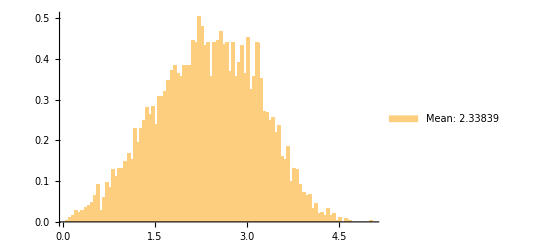
-Graphics-i.i.d Complex Gaussian Channel

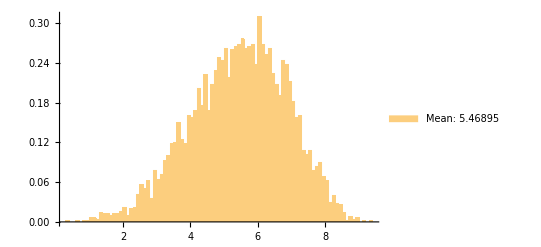
-Graphics-Chaotic Channel

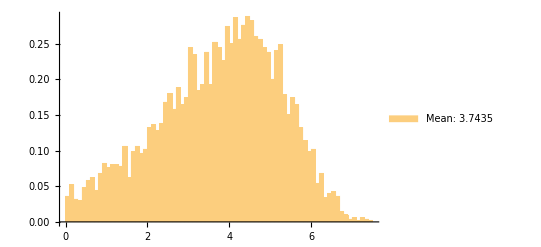
-Graphics-Correlative Channel

```mathematica
singleUser=RandomChoice[users];
CH1Rand:=CH1[[All,singleUser]];
CH2Rand:=CH2[[All,singleUser]];
CH3Rand:=CH3[[All,singleUser]];
rate2CH1:=Log2[1+P*Norm[CH1Rand]^2];
rate2CH2:=Log2[1+P*Norm[CH2Rand]^2];
rate2CH3:=Log2[1+P*Norm[CH3Rand]^2];
Labeled[Histogram[ParallelTable[rate2CH1,{repeat}],80,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[rate2CH2,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[rate2CH3,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rate2CH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

2. 	The BS chooses to transmit to a single user with the strongest channel (the user with the highest row norm) and transmits to it at maximum power.

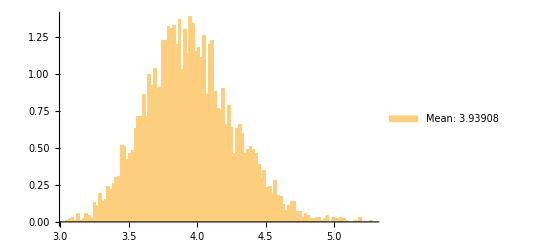
-Graphics-i.i.d Complex Gaussian Channel

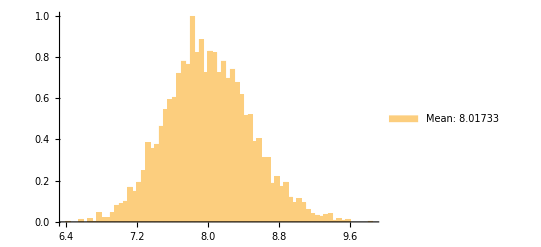
-Graphics-Chaotic Channel

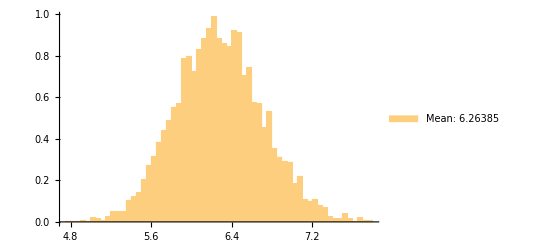
-Graphics-Correlative Channel

```mathematica
rateStrongCH1:=Log2[1+P*Max[Table[Norm[CH1[[All,i]]]^2,{i,k}]]];
rateStrongCH2:=Log2[1+P*Max[Table[Norm[CH2[[All,i]]]^2,{i,k}]]];
rateStrongCH3:=Log2[1+P*Max[Table[Norm[CH3[[All,i]]]^2,{i,k}]]];
Labeled[Histogram[ParallelTable[rateStrongCH1,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[rateStrongCH2,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[rateStrongCH3,{repeat}],80,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[rateStrongCH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

3. 	The BS chooses to transmit to 𝑡 randomly chosen users using ZFBF with uniform power allocation between the selected users .

```mathematica
Puniformal = P/t// N;
multiUsers = RandomSample[users,t];
CH1Trand:=Table[CH1[[All,multiUsers[[i]]]],{i,t}];
CH2Trand:=Table[CH2[[All,multiUsers[[i]]]],{i,t}];
CH3Trand:=Table[CH3[[All,multiUsers[[i]]]],{i,t}];
ratetRand1:=rateFunc[Puniformal,CH1Trand,Transpose[Map[Normalize,Transpose[PseudoInverse[CH1Trand]]]], t];
ratetRand2:=rateFunc[Puniformal,CH2Trand,Transpose[Map[Normalize,Transpose[PseudoInverse[CH2Trand]]]], t];
ratetRand3:=rateFunc[Puniformal,CH3Trand,Transpose[Map[Normalize,Transpose[PseudoInverse[CH3Trand]]]], t];
```

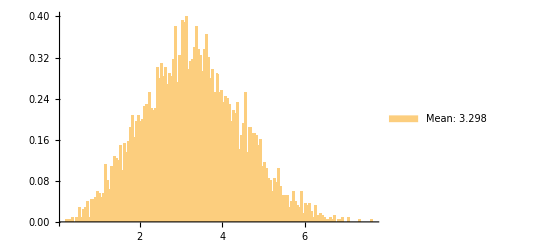
-Graphics-i.i.d Complex Gaussian Channel

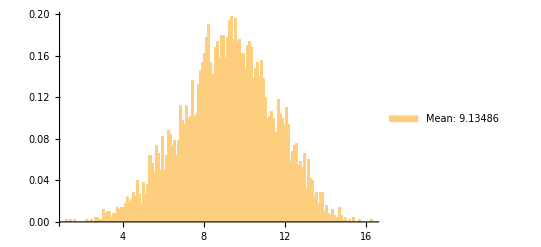
-Graphics-Chaotic Channel

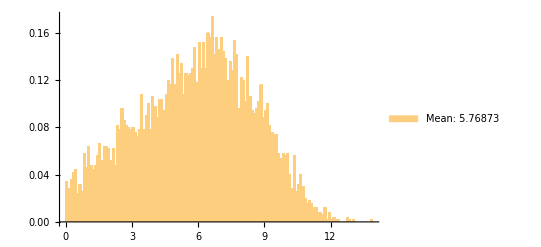
-Graphics-Correlative Channel

```mathematica
(*Output grahp*)
Labeled[Histogram[ParallelTable[ratetRand1,{repeat}],120,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[ratetRand2,{repeat}],120,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[ratetRand3,{repeat}],120,"PDF",
ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetRand3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

4.  The base station chooses to transmit to the t strongest users using ZFBF, so that the power is equally distributed between the selected users .

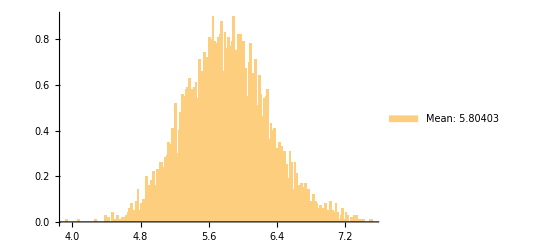
-Graphics-i.i.d Complex Gaussian Channel

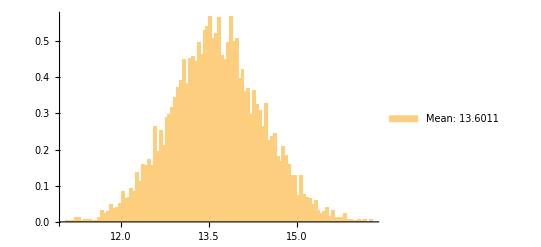
-Graphics-Chaotic Channel

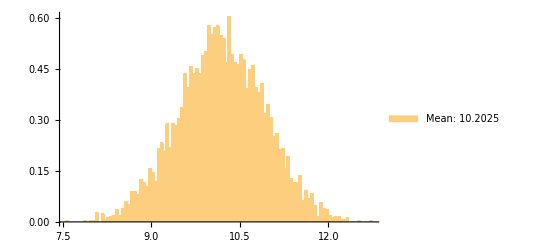
-Graphics-Correlative Channel

```mathematica
ratetStrongestCH1:=rateStrongFunc[Puniformal,StrongestNorm[t,CH1],t];
ratetStrongestCH2:=rateStrongFunc[Puniformal,StrongestNorm[t,CH2],t];
ratetStrongestCH3:=rateStrongFunc[Puniformal,StrongestNorm[t,CH3],t];
Labeled[Histogram[ParallelTable[ratetStrongestCH1,{repeat}],120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH1,{repeat}]//N]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[ParallelTable[ratetStrongestCH2,{repeat}],120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH2,{repeat}]//N]]},Bottom]],"Chaotic Channel",Top]
Labeled[Histogram[ParallelTable[ratetStrongestCH3,{repeat}],120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[ParallelTable[ratetStrongestCH3,{repeat}]//N]]},Bottom]],"Correlative Channel",Top]
```

5. The BS tests all user subgroups of the size 𝑡, and transmits to the optimal group (e.g., with the highest rates) using ZFBF. The power allocation is uniform between the selected users.

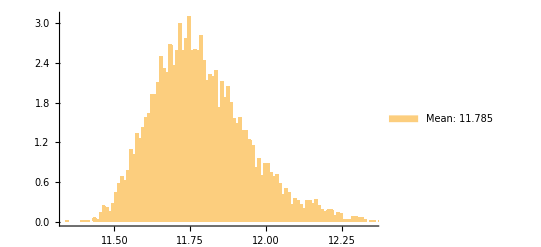
-Graphics-i.i.d Complex Gaussian Channel

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

```mathematica
t = 2;
SubGroupst =Subsets[users, {t}];
L=Length[SubGroupst];
ListNumGroup = Table[i,{i,L}];
(*Using the function from qustion 3*)
OptimalGroupRateCH1:=Max[Table[rateFunc[Puniformal,CH1,Transpose[Map[Normalize,Transpose[PseudoInverse[SubgroupCh[t,L,CH1,SubGroupst][[j]]]]]] , t],{j,L}]];
res1=ParallelTable[OptimalGroupRateCH1,{repeat}];
Labeled[Histogram[res1,120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res1]]},Bottom]],"i.i.d Complex Gaussian Channel",Top]
OptimalGroupRateCH2:=Max[Table[rateFunc[Puniformal,CH2,Transpose[Map[Normalize,Transpose[PseudoInverse[SubgroupCh[t,L,CH2,SubGroupst][[j]]]]]] , t],{j,L}]];
res2=ParallelTable[OptimalGroupRateCH2,{repeat}];
Labeled[Histogram[res2,120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res2]]},Bottom]],"Chaotic Channel",Top]
OptimalGroupRateCH3:=Max[Table[rateFunc[Puniformal,CH3,Transpose[Map[Normalize,Transpose[PseudoInverse[SubgroupCh[t,L,CH3,SubGroupst][[j]]]]]]  , t],{j,L}]];
res3=ParallelTable[OptimalGroupRateCH3,{repeat}];
Labeled[Histogram[res3,120,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[res3]]},Bottom]],"Correlative Channel",Top]
```

#### Bonus

SUS Algorithm

```mathematica
(*Example complex-valued channel matrix*)
```

```mathematica
t=2;
channel1=Table[
(* channel matrix*)
channelMatrix=Transpose[CH1];
(*Select the channel responses of the selected users, The user whit the max Norm*)
nullSpace=NullSpace[{channelMatrix[[MaxNormUser[channelMatrix]]]}];(*Calculate the null space of the selected channel matrix*)
selectedUsers={MaxNormUser[channelMatrix]};
projections=nullSpace.ConjugateTranspose[channelMatrix];
maxNormUser2:=Position[Norm/@Transpose[projections],Max[Norm/@Transpose[projections]]][[1,1]];
selectedUsers=Append[selectedUsers,maxNormUser2];
nullSpace=Append[nullSpace,NullSpace[{channelMatrix[[maxNormUser2]]}][[1]]];
nullSpace= NullSpace[{nullSpace[[1]]}][[1]];
selectedUsers=DeleteDuplicates[selectedUsers];
If[Length[selectedUsers] == 1,selectedUsers=Append[selectedUsers,MaxNormUser[Transpose[nullSpace]]],Else[Continue]];
selectedUsers=DeleteDuplicates[selectedUsers];
TotalRate[channelMatrix,selectedUsers],{5000}];

channel2=Table[
(* channel matrix*)
channelMatrix=Transpose[CH2];
(*Select the channel responses of the selected users, The user whit the max Norm*)
nullSpace=NullSpace[{channelMatrix[[MaxNormUser[channelMatrix]]]}];(*Calculate the null space of the selected channel matrix*)
selectedUsers={MaxNormUser[channelMatrix]};
projections=nullSpace.ConjugateTranspose[channelMatrix];
maxNormUser2:=Position[Norm/@Transpose[projections],Max[Norm/@Transpose[projections]]][[1,1]];
selectedUsers=Append[selectedUsers,maxNormUser2];
nullSpace=Append[nullSpace,NullSpace[{channelMatrix[[maxNormUser2]]}][[1]]];
nullSpace= NullSpace[{nullSpace[[1]]}][[1]];
selectedUsers=DeleteDuplicates[selectedUsers];
If[Length[selectedUsers] == 1,selectedUsers=Append[selectedUsers,MaxNormUser[Transpose[nullSpace]]],Else[Continue]];
selectedUsers=DeleteDuplicates[selectedUsers];
Totalrate[channelMatrix,selectedUsers],{5000}];

channel3=Table[
(* channel matrix*)
channelMatrix=Transpose[CH3];
(*Select the channel responses of the selected users, The user whit the max Norm*)
nullSpace=NullSpace[{channelMatrix[[MaxNormUser[channelMatrix]]]}];(*Calculate the null space of the selected channel matrix*)
selectedUsers={MaxNormUser[channelMatrix]};
projections=nullSpace.ConjugateTranspose[channelMatrix];
maxNormUser2:=Position[Norm/@Transpose[projections],Max[Norm/@Transpose[projections]]][[1,1]];
selectedUsers=Append[selectedUsers,maxNormUser2];
nullSpace=Append[nullSpace,NullSpace[{channelMatrix[[maxNormUser2]]}][[1]]];
nullSpace= NullSpace[{nullSpace[[1]]}][[1]];
selectedUsers=DeleteDuplicates[selectedUsers];
If[Length[selectedUsers] == 1,selectedUsers=Append[selectedUsers,MaxNormUser[Transpose[nullSpace]]],Else[Continue]];
selectedUsers=DeleteDuplicates[selectedUsers];
Totaleate[channelMatrix,selectedUsers],{5000}];
```

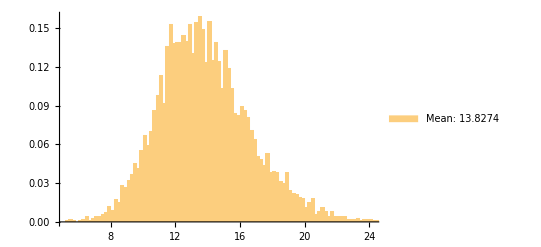
-Graphics-SUS i.i.d Complex Gaussian Channel

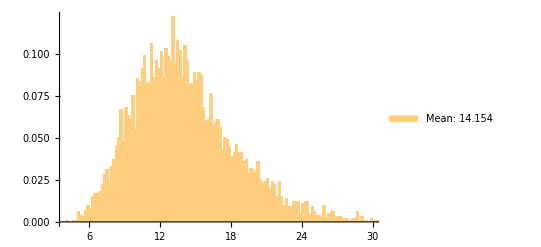
-Graphics-SUS Chaotic Channel

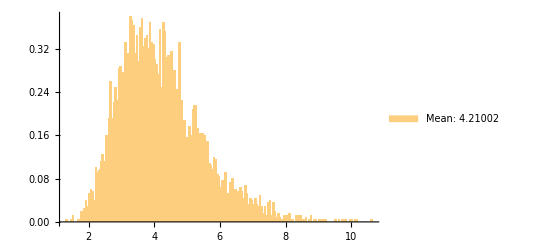
-Graphics-SUS Correlative Channel

```mathematica
Labeled[Histogram[channel1,150,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[channel1]]},Bottom]],"SUS i.i.d Complex Gaussian Channel",Top]
Labeled[Histogram[channel2,150,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[channel2]]},Bottom]],"SUS Chaotic Channel",Top]
Labeled[Histogram[channel3,150,"PDF",ChartLegends->Placed[{StringForm["Mean: ``",Mean[channel3]]},Bottom]],"SUS Correlative Channel",Top]
```

```mathematica
(*Select the channel responses of the selected users, The user whit the max Norm*)
nullSpace=NullSpace[{channelMatrix[[MaxNormUser[channelMatrix]]]}];(*Calculate the null space of the selected channel matrix*)
selectedUsers={MaxNormUser[channelMatrix]};
projections=nullSpace.ConjugateTranspose[channelMatrix];
maxNormUser2:=Position[Norm/@Transpose[projections],Max[Norm/@Transpose[projections]]][[1,1]]selectedUsers=Append[selectedUsers,maxNormUser2];
nullSpace=Append[nullSpace,NullSpace[{channelMatrix[[maxNormUser2]]}][[1]]];
nullSpace= NullSpace[{nullSpace[[1]]}][[1]];
selectedUsers=DeleteDuplicates[selectedUsers];
```

## part 2 - simulation

```mathematica
(*Transmission power in Watts*)
P=5;  
Mr=4;   
Mt=4;
M = 5000;
Listplot ={};
Puniformal = P/Mt;
(*Symbol range*)
Uniform = Table[i, {i,-4,4}] ;
(*Channel*)
ChannelGaussian=Table[RandomVariate[NormalDistribution[0,1]] ,{Mr},{Mt}];
Print["Channel - Gaussian Channel"]
ChannelGaussian//MatrixForm
```

Channel - Gaussian Channel

(-1.79815 | 0.50663 | -1.53157 | 0.341243
-2.32823 | 0.381378 | -1.90116 | -0.581637
-1.31469 | 2.18133 | 0.743005 | -0.587088
-0.978513 | -1.08541 | 0.777555 | -0.807449)

#### Function

```mathematica
MSE[H_,Hest_,Mr_,Mt_,M_] := ∑_(i=1)^M (NormaL2[(H - Hest[[i]])]^2/(Mr*Mt*M));
NormaL2[Vect_]:=√(∑_(j=1)^(Dimensions[Vect][[1]]) ∑_(i=1)^(Dimensions[Vect][[2]]) (Vect[[j]][[i]])^2)
```

#### Simulation 1

N = Mr = 4

```mathematica
Mr=4;
(*Matrix size 4x4*)
ListSymbol1 := Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol:=ListSymbol1/Norm[ListSymbol1] //N;
(*Transmited*)
tembel:=√Puniformal*NormaListSymbol;
Y:= ChannelGaussian.tembel+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
Hest=ParallelTable[Y.PseudoInverse[tembel],{M}];
S1=MSE[tembel,Hest,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S1]]
```

{29.3156}

#### Simulation 2

N = Mr + 1= 5

```mathematica
Mr=5;
(*Matrix size 4x5*)
ListSymbol2 := Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol2:=ListSymbol2/Norm[ListSymbol2] //N ;
(*Transmited*)
tembel2:=√Puniformal*NormaListSymbol2;
Y2:= ChannelGaussian.tembel2+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol2=ParallelTable[Y2.PseudoInverse[tembel2],{M}];
S2=MSE[ChannelGaussian,TableSymbol2,Mr,Mt,M];
Listplot=Append[Listplot,10*Log10[S2]]
```

{29.3156,13.7484}

#### Simulation 3

N = Mr + 2 = 6

```mathematica
Mr=6;
(*Matrix size 4x6*)
ListSymbol3 := Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol3:=ListSymbol3/Norm[ListSymbol3] //N ;
(*Transmited*)
tembel3:=√Puniformal*NormaListSymbol3;
Y3:= ChannelGaussian.tembel3+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol3=ParallelTable[Y3.PseudoInverse[tembel3],{M}];
S3=MSE[ChannelGaussian,TableSymbol3,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S3]]
```

{29.3156,13.7484,7.68148}

#### Simulation 4

N = Mr + 3 = 7

```mathematica
Mr=7;
(*Matrix size 4x7*)
ListSymbol4:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol4:=ListSymbol4/Norm[ListSymbol4] //N ;
(*Transmited*)
tembel4:=√Puniformal*NormaListSymbol4;
Y4:= ChannelGaussian.tembel4+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol4=ParallelTable[Y4.PseudoInverse[tembel4],{M}];
S4=MSE[ChannelGaussian,TableSymbol4,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S4]]
```

{29.3156,13.7484,7.68148,5.11077}

#### Simulation 5

N = Mr + 4 = 8

```mathematica
Mr=8;
(*Matrix size 4x8*)
ListSymbol5:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol5:=ListSymbol5/Norm[ListSymbol5] //N ;
(*Transmited*)
tembel5:=√Puniformal*NormaListSymbol5;
Y5:= ChannelGaussian.tembel5+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol5=ParallelTable[Y5.PseudoInverse[tembel5],{M}];
S5=MSE[ChannelGaussian,TableSymbol5,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S5]]
```

{29.3156,13.7484,7.68148,5.11077,3.51889}

#### Simulation 6

N = Mr + 4 = 9

```mathematica
Mr=9;
(*Matrix size 4x9*)
ListSymbol6:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol6:=ListSymbol6/Norm[ListSymbol6] //N ;
(*Transmited*)
tembel6:=√Puniformal*NormaListSymbol6;
Y6:= ChannelGaussian.tembel6+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol6=ParallelTable[Y6.PseudoInverse[tembel6],{M}];
S6=MSE[ChannelGaussian,TableSymbol6,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S6]]
```

{29.3156,13.7484,7.68148,5.11077,3.51889,2.37426}

#### Simulation 6-20

```mathematica
Mr=10;
(*Matrix size 4x10*)
ListSymbol7:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol7:=ListSymbol7/Norm[ListSymbol7] //N ;
(*Transmited*)
tembel7:=√Puniformal*NormaListSymbol7;
Y7:= ChannelGaussian.tembel7+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol7=ParallelTable[Y7.PseudoInverse[tembel7],{M}];
S7=MSE[ChannelGaussian,TableSymbol7,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S7]];
Mr=11;
(*Matrix size 4x11*)
ListSymbol8:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol8:=ListSymbol8/Norm[ListSymbol8] //N ;
(*Transmited*)
tembel8:=√Puniformal*NormaListSymbol8;
Y8:= ChannelGaussian.tembel8+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol8=ParallelTable[Y8.PseudoInverse[tembel8],{M}];
S8=MSE[ChannelGaussian,TableSymbol8,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S8]];
Mr=12;
(*Matrix size 4x12*)
ListSymbol9:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol9:=ListSymbol9/Norm[ListSymbol9] //N ;
(*Transmited*)
tembel9:=√Puniformal*NormaListSymbol9;
Y9:= ChannelGaussian.tembel9+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol9=ParallelTable[Y9.PseudoInverse[tembel9],{M}];
S9=MSE[ChannelGaussian,TableSymbol9,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S9]];
Mr=13;
(*Matrix size 4x13*)
ListSymbol10:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol10:=ListSymbol10/Norm[ListSymbol10] //N ;
(*Transmited*)
tembel10:=√Puniformal*NormaListSymbol10;
Y10:= ChannelGaussian.tembel10+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol10=ParallelTable[Y10.PseudoInverse[tembel10],{M}];
S10=MSE[ChannelGaussian,TableSymbol10,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S10]];
Mr=14;
(*Matrix size 4x14*)
ListSymbol11:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol11:=ListSymbol11/Norm[ListSymbol11] //N ;
(*Transmited*)
tembel11:=√Puniformal*NormaListSymbol11;
Y11:= ChannelGaussian.tembel11+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol11=ParallelTable[Y11.PseudoInverse[tembel11],{M}];
S11=MSE[ChannelGaussian,TableSymbol11,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S11]];
Mr=15;
(*Matrix size 4x15*)
ListSymbol12:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol12:=ListSymbol12/Norm[ListSymbol12] //N ;
(*Transmited*)
tembel12:=√Puniformal*NormaListSymbol12;
Y12:= ChannelGaussian.tembel12+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol12=ParallelTable[Y12.PseudoInverse[tembel12],{M}];
S12=MSE[ChannelGaussian,TableSymbol12,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S12]];
Mr=16;
(*Matrix size 4x16*)
ListSymbol13:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol13:=ListSymbol13/Norm[ListSymbol13] //N ;
(*Transmited*)
tembel13:=√Puniformal*NormaListSymbol13;
Y13:= ChannelGaussian.tembel13+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol13=ParallelTable[Y13.PseudoInverse[tembel13],{M}];
S13=MSE[ChannelGaussian,TableSymbol13,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S13]];
Mr=17;
(*Matrix size 4x17*)
ListSymbol14:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol14:=ListSymbol14/Norm[ListSymbol14] //N ;
(*Transmited*)
tembel14:=√Puniformal*NormaListSymbol14;
Y14:= ChannelGaussian.tembel14+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol14=ParallelTable[Y14.PseudoInverse[tembel14],{M}];
S14=MSE[ChannelGaussian,TableSymbol14,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S14]];
Mr=18;
(*Matrix size 4x18*)
ListSymbol15:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol15:=ListSymbol15/Norm[ListSymbol15] //N ;
(*Transmited*)
tembel15:=√Puniformal*NormaListSymbol15;
Y15:= ChannelGaussian.tembel15+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol15=ParallelTable[Y15.PseudoInverse[tembel15],{M}];
S15=MSE[ChannelGaussian,TableSymbol15,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S15]];
Mr=19;
(*Matrix size 4x19*)
ListSymbol16:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol16:=ListSymbol16/Norm[ListSymbol16] //N ;
(*Transmited*)
tembel16:=√Puniformal*NormaListSymbol16;
Y16:= ChannelGaussian.tembel16+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol16=ParallelTable[Y16.PseudoInverse[tembel16],{M}];
S16=MSE[ChannelGaussian,TableSymbol16,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S16]];
Mr=20;
(*Matrix size 4x20*)
ListSymbol17:= Table[RandomChoice[Uniform],{Mt},{Mr}];
(*Normalization ListSymbol*)
NormaListSymbol17:=ListSymbol17/Norm[ListSymbol17] //N ;
(*Transmited*)
tembel17:=√Puniformal*NormaListSymbol17;
Y17:= ChannelGaussian.tembel17+Table[RandomVariate[NormalDistribution[0,0.5]] ,{Mt},{Mr}];
TableSymbol17=ParallelTable[Y17.PseudoInverse[tembel17],{M}];
S17=MSE[ChannelGaussian,TableSymbol17,Mr,Mt,M];
(*Volt to dB*)
Listplot=Append[Listplot,10*Log10[S17]];
```

{29.3156,13.7484,7.68148,5.11077,3.51889,2.37426,1.47505,0.709166,0.103037,-0.426079,-0.940003,-1.39308,-1.77232,-2.12507,-2.46526,-2.82346,-3.07453}

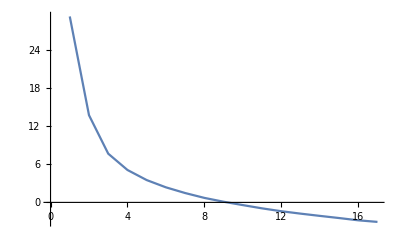

```mathematica
Listplot
ListLinePlot[Listplot]
```